```mathematica
x[t_]:=UnitStep[t-1]*(1-UnitStep[t-2])
```

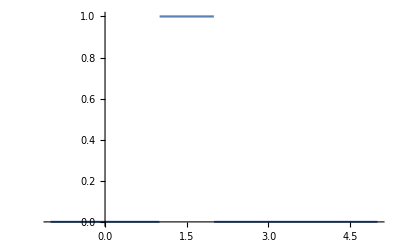

```mathematica
Plot[x[t],{t,-1,5}]
```

```mathematica
h[t_]:=UnitStep[t]*Piecewise[{{1/Exp[t-1],True}},1]
```

```mathematica
Dynamic@Plot[h[t],{t,-1,5}]
```

```mathematica
y=Convolve[h[t],x[t],t,u];
```

```mathematica
Dynamic@Plot[y,{u,-1,5}]
```

```mathematica
Inverse[Integrate[f[t],t]]
```

Inverse[∫f[t]ⅆt]

```mathematica
Echo[Simplify@InverseLaplaceTransform[1/(s(s+1)(s-5)),s,t]];
Plot[Re[%],{t,0,10}]
```

1/30 ⅇ^-t (5-6 ⅇ^t+ⅇ^(6 t))

-Graphics-

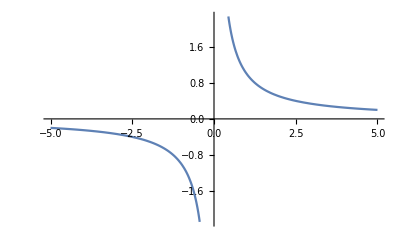

```mathematica
Plot[1/x,{x,-5,5}]
```

```mathematica
InverseLaplaceTransform[1/(s+4),s,t]
```

ⅇ^(-4 t)

```mathematica
LaplaceTransform[DiracDelta[t],t,s]
```

1

```mathematica
fs = k(2y[t]+x[t])
fd=-c y'[t]
```

k ((1-UnitStep[-2+t]) UnitStep[-1+t]+2 (Piecewise[{{(-1+ⅇ) ⅇ^(2-u), u≥2}, {ⅇ-ⅇ^(2-u), 1≤u<2}, {0, True}}])[t])

-c (Piecewise[{{(-1+ⅇ) ⅇ^(2-u), u≥2}, {ⅇ-ⅇ^(2-u), 1≤u<2}, {0, True}}])'[t]

```mathematica
diffeq=m y''[t]==fs+fd
```

m (Piecewise[{{(-1+ⅇ) ⅇ^(2-u), u≥2}, {ⅇ-ⅇ^(2-u), 1≤u<2}, {0, True}}])''[t]==k ((1-UnitStep[-2+t]) UnitStep[-1+t]+2 (Piecewise[{{(-1+ⅇ) ⅇ^(2-u), u≥2}, {ⅇ-ⅇ^(2-u), 1≤u<2}, {0, True}}])[t])-c (Piecewise[{{(-1+ⅇ) ⅇ^(2-u), u≥2}, {ⅇ-ⅇ^(2-u), 1≤u<2}, {0, True}}])'[t]

```mathematica
DSolve[diffeq,{y[t]},{t}];
```

```mathematica
LaplaceTransform[diffeq,t,s]
```

m (s^2 LaplaceTransform[(Piecewise[{{(-1+ⅇ) ⅇ^(2-u), u≥2}, {ⅇ-ⅇ^(2-u), 1≤u<2}, {0, True}}])[t],t,s]-s (Piecewise[{{(-1+ⅇ) ⅇ^(2-u), u≥2}, {ⅇ-ⅇ^(2-u), 1≤u<2}, {0, True}}])[0]-(Piecewise[{{(-1+ⅇ) ⅇ^(2-u), u≥2}, {ⅇ-ⅇ^(2-u), 1≤u<2}, {0, True}}])'[0])==-(ⅇ^(-2 s) k)/s+(ⅇ^-s k)/s+2 k LaplaceTransform[(Piecewise[{{(-1+ⅇ) ⅇ^(2-u), u≥2}, {ⅇ-ⅇ^(2-u), 1≤u<2}, {0, True}}])[t],t,s]-c (s LaplaceTransform[(Piecewise[{{(-1+ⅇ) ⅇ^(2-u), u≥2}, {ⅇ-ⅇ^(2-u), 1≤u<2}, {0, True}}])[t],t,s]-(Piecewise[{{(-1+ⅇ) ⅇ^(2-u), u≥2}, {ⅇ-ⅇ^(2-u), 1≤u<2}, {0, True}}])[0])

## Inclass

## Pass 1

```mathematica
ms=LaplaceTransform[Sin[ω/(2π)t]*UnitStep[t],t,s]
sol=Simplify[InverseLaplaceTransform[-k/(m s^2 + k+c s)*ms,s,t]]*UnitStep[t];
```

(2 π ω)/(4 π^2 s^2+ω^2)

```mathematica
Manipulate[
p={k->3,m->1,c->.1,ω->ω1},{ω1,0,15}]
Dynamic[sol2=sol/.p;
lines={sol2,D[sol2,t],D[sol2,{t,2}]};
Plot[Evaluate@lines[[1]],{t,0,100},PlotRange->20{-1,1},PlotLegends->{"x","v","a"},ImageSize->Large]]
```